```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["SQLite"];
conn = OpenSQLConnection[JDBC["SQLite", "/Users/erinhengel/Dropbox/Readability/dta/read.db"]];
font="Optima";
```

/Users/erinhengel/Dropbox/Readability/draft/pdf/figure7.pdf

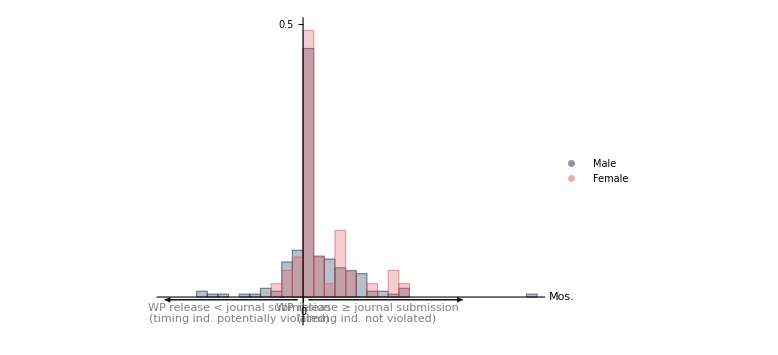

```mathematica
sql="
SELECT 
	ArticleID, NberID, (JULIANDAY(WPDate)-JULIANDAY(Received))/30 AS ReleaseSubmit,
	SUM(Sex) AS Male, COUNT(AuthorID) AS N
	FROM Article
	NATURAL JOIN AuthorCorr
	NATURAL JOIN Author
	NATURAL JOIN NBERCorr
	NATURAL JOIN (SELECT NberID, WPDate FROM Nber) AS Nber
	WHERE Received IS NOT NULL
	GROUP BY ArticleID, NberID
";
data= SQLExecute[conn, sql];
male=Select[data,#⟦4⟧==#⟦5⟧&]⟦All,3⟧;
female=Select[data,#⟦4⟧<#⟦5⟧&]⟦All,3⟧;
opacity=Opacity[0.3];
{blue,pink}={RGBColor[26/255,40/255,78/255],RGBColor[216/255,92/255,99/255]};
legend=PointLegend[{blue,pink},{"Male","Female"},
LegendMarkers->Graphics[{EdgeForm[None],Opacity[0.5],Disk[]}],
LegendMarkerSize->10,
LabelStyle->{FontSize->16,FontColor->Gray,FontFamily->font},
LegendMargins->5,
LegendLayout->"Row"
];
histogram=Histogram[{male,female},{5},"Probability",
ChartStyle->{
Directive[blue,opacity],
Directive[pink,opacity]},
ChartLegends->Placed[legend,{Right,Center}],
AxesStyle->Directive[Thin,Gray,FontFamily->font,FontSize->Medium],
Ticks->{{0},{0.5}},
AxesOrigin->{0,0},
Epilog->{
{Thickness[Tiny],Arrowheads[Small],
Arrow[{{2.5,-0.005},{75,-0.005}}],
Arrow[{{-2.5,-0.005},{-65,-0.005}}]},
Text[Style["WP release ≥ journal submission\n(timing ind. not violated)",Gray,FontFamily->font,FontSize->Small],{30,-0.03}],
Text[Style["WP release < journal submission\n(timing ind. potentially violated)",Gray,FontFamily->font,FontSize->Small],{-30,-0.03}]
}];
plot=Show[
{histogram},
PlotRange->{{-65,110},{-0.04,0.5}},
AxesLabel->{"Mos.",None},
LabelStyle->{FontSize->14},
ImageSize->Full
];
Export["/Users/erinhengel/Dropbox/Readability/draft/pdf/figure7.pdf",plot]
Export["/Users/erinhengel/Dropbox/Readability/presentation/COSME/pdf/figure7.pdf",plot];
Show[plot,ImageSize->Large]
```